```mathematica
safeClebschGordan[{j1_,m1_},{j2_,m2_},{j_,m_}]:=If[Abs[j1-j2]≤j≤j1+j2&&m1+m2==m
&&-j1≤m1≤j1&&-j2≤m2≤j2&&-j≤m≤j,
ClebschGordan[{j1,m1},{j2,m2},{j,m}],
0];
```

```mathematica
safeClebschGordan[{1,1},{1,-1},{1,0}]
```

1/(√2)

```mathematica
safeClebschGordan[{1,1},{1,0},{1,1}]
```

1/(√2)

```mathematica
ClearAll[σRes]
σRes[inA_,i3A_,inB_,i3B_,res_,eCM_]:=
Block[{ΓresAB=Γ[res,{inA,inB},eCM]},
If[ΓresAB≤0||eCM≤m0[inA]+m0[inB],0,safeClebschGordan[{isoSpin[inA],i3A},{isoSpin[inB],i3B},{isoSpin[res],i3A+i3B}]^2
*(2j[res]+1)/((2j[inA]+1)(2j[inB]+1)) 
*Pi/pCMS[eCM,m0[inA],m0[inB]]^2 
(**BR[res,{inA,inB}]*Γ[res,eCM]*)* Γ[res,{inA,inB},eCM]
* breitWigner[Γ[res,eCM],m0[res]-eCM]

]
];

σRes[inA_,i3A_,inB_,i3B_,eCM_]:=
Sum[σRes[inA,i3A,inB,i3B,res,eCM]
,{res,Join[Ds,Ns,Ms]}
];
```

```mathematica
σRes[N938,1/2,pi,0,D1232,1.5]
```

37.3443

```mathematica
Γ[D1232,1.5]
```

0.470773

```mathematica
Block[{i3A=1,i3B=1,res=rho},
safeClebschGordan[{isoSpin[pi],i3A},{isoSpin[pi],i3B},{isoSpin[res],i3A+i3B}]
]
```

```mathematica
ptsTot=Monitor[
Block[{hA=N938,i3A=+1/2,hB=pi,i3B=-1},
Table[{
pLab[m0@hB,m0@hA,eCM],
σRes[hA,i3A,hB,i3B,eCM]},{eCM,1.,3.,0.01}]
],{res,ProgressIndicator[eCM,{1.,3.}]}
];
ListLinePlot[ptsTot,PlotRange->All]
```

ListLinePlot::lpn: $Aborted is not a list of numbers or pairs of numbers.

ListLinePlot[$Aborted,PlotRange→All]

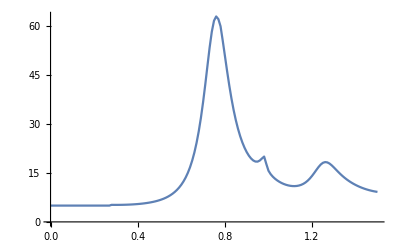

```mathematica
ptsTot=Monitor[
Block[{hA=pi,i3A=+1,hB=pi,i3B=-1},
Table[{
eCM+0pLab[m0@hB,m0@hA,eCM],
5+σRes[hA,i3A,hB,i3B,eCM]},{eCM,0.,1.5,0.01}]
],{res,ProgressIndicator[eCM,{0.,1.5}]}
];
ListLinePlot[ptsTot,PlotRange->All]
```

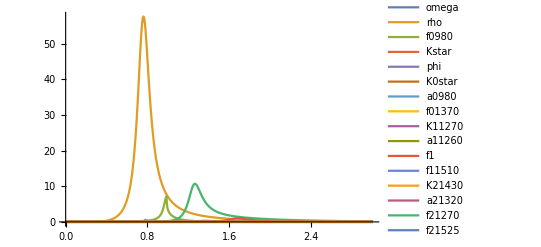

```mathematica
pts=Monitor[
Block[{hA=pi,hB=pi},
Table[{
res,Table[{
eCM+0pLab[m0[hB],m0[hA],eCM],
σRes[hA,1,hB,-1,res,eCM]},{eCM,0.,3.,0.005}]
},{res,Ms}]
],{res,ProgressIndicator[eCM,{0.,3.}]}
];
ListLinePlot[Second/@pts,PlotLegends->First/@pts,PlotRange->All]
```

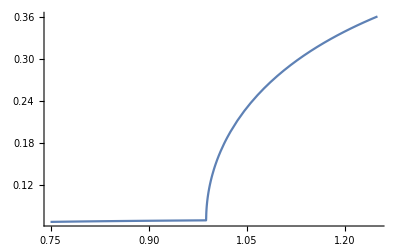

```mathematica
Plot[Γ[f0980,eCM],{eCM,0.75,1.25},PlotRange->All]
```

```mathematica
σRes[pi,1,pi,0,1.5]
```

3.3928

```mathematica
ptsTot=Monitor[
Block[{hA=pi,hB=pi},
Table[{
eCM,
σRes[hA,hB,eCM]},{eCM,0.,3.,0.01}]
],{ProgressIndicator[eCM,{0.,3.}],res}
];
ListLinePlot[ptsTot,PlotRange->All]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
pts=Monitor[
Table[{mes,Table[{eCM,a[mes,eCM]},{eCM,0.,5.,0.1}]},{mes,Ms}],
mes];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {0.779067}. NIntegrate obtained 6.32659 and 0.0000517053 for the integral and error estimates.

Calculating aN for omega

Calculating aN for rho

NIntegrate::inumri: The integrand breitWigner[Γ[f0980,{Ka,Ka},m]+Γ[f0980,{pi,pi},m],0.98-m] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,1.276}}.

Calculating aN for f0980

NIntegrate::inumri: The integrand breitWigner[Γ[f0980,{Ka,Ka},m]+Γ[f0980,{pi,pi},m],0.98-m] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,1.276}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

Assert::asrtf: Assertion p0res$5799943>0&&p0res1$5799943>0 failed.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Assert::asrtf: Assertion p0res$5801903>0&&p0res1$5801903>0 failed.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Assert::asrtf: Assertion p0res$5803677>0&&p0res1$5803677>0 failed.

General::stop: Further output of Assert::asrtf will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Calculating aN for Kstar

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {1.01351}. NIntegrate obtained 6.83079 and 0.0251673 for the integral and error estimates.

Calculating aN for phi

Calculating aN for K0star

Calculating aN for a0980

Calculating aN for f01370

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in m near {m} = {143.722}. NIntegrate obtained 6.76806 and 0.000150068 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

Calculating aN for K11270

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

Calculating aN for a11260

Calculating aN for f1

Calculating aN for f11510

Calculating aN for K21430

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Calculating aN for a21320

Calculating aN for f21270

Calculating aN for f21525

Calculating aN for K11400

Calculating aN for b11235

Calculating aN for h11170

Calculating aN for h11380

Calculating aN for Kstar1410

Calculating aN for rho1465

Calculating aN for omega1419

Calculating aN for phi1680

Calculating aN for Kstar1680

Calculating aN for rho1700

Calculating aN for omega1662

Calculating aN for phi1900

```mathematica
ListLinePlot[Second/@pts,PlotLegends->First/@pts]
```

NIntegrate::inumri: The integrand breitWigner[Γ[f0980,{Ka,Ka},m]+Γ[f0980,{pi,pi},m],0.98-m] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,1.276}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

$Aborted

```mathematica
Plot[
Evaluate@Table[
Γ[mes,eCM],{mes,Ms}
],
{eCM,0.,5.}]
```

$Aborted

```mathematica
pts
```

NIntegrate::inumri: The integrand breitWigner[Γ[f0980,{Ka,Ka},m]+Γ[f0980,{pi,pi},m],0.98-m] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,1.276}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

NIntegrate::inumri: The integrand breitWigner[Γ[f0980,{Ka,Ka},m]+Γ[f0980,{pi,pi},m],0.98-m] has evaluated to Overflow, Indeterminate, or Infinity for all sampling points in the region with boundaries {{∞,1.276}}.

General::stop: Further output of NIntegrate::inumri will be suppressed during this calculation.

{{omega,{{0.,0.158063 breitWigner[0,0.782]},{0.1,0.158063 breitWigner[0,0.682]},{0.2,4.15385×10^-6},{0.3,0.0000471308},44,{4.8,0.000502752},{4.9,0.000480426},{5.,0.000459535}}},26,{phi1900,1}}
 |  |  |  |